```mathematica
SetDirectory["/home/ebg/Documents/2_Latex/CAMDA"]
```

/home/ebg/Documents/2_Latex/CAMDA

```mathematica
dat00=Import["CAMDA(v).dat","Table"];
nOTU=Length[dat00]-1
```

20448

```mathematica
borrar=Transpose[dat00];
nCTY=Length[borrar]-1
```

365

```mathematica
dat=Table[dat00[[i,j]],{i,1,5},{j,1,nCTY+1}];
TableForm[dat]
```

ID | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | MIN | MIN | MIN | MIN | MIN | MIN | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH
468 | 1756 | 785 | 29 | 5 | 57 | 7 | 6 | 2 | 336 | 3 | 22 | 5 | 5 | 7 | 2228 | 373 | 1072 | 626 | 1358 | 3021 | 113 | 121 | 55 | 62 | 845 | 58 | 37 | 397 | 3878 | 1872 | 1271 | 2813 | 1709 | 2909 | 1792 | 2072 | 4050 | 5156 | 1520 | 1178 | 2776 | 1810 | 2339 | 1687 | 18 | 7 | 18 | 10 | 28 | 73 | 44 | 397 | 6 | 8 | 142 | 3 | 277 | 17 | 18 | 5 | 13 | 56 | 20 | 275 | 31 | 6 | 374 | 268 | 805 | 104 | 91 | 77 | 84 | 88 | 106 | 87 | 120 | 86 | 76 | 3778 | 44 | 4189 | 22 | 2315 | 1327 | 30 | 521 | 61 | 5841 | 1593 | 75 | 173 | 218 | 2694 | 338 | 148 | 1985 | 226 | 379 | 136 | 776 | 273 | 135 | 160 | 797 | 124 | 862 | 44 | 841 | 9768 | 1211 | 11614 | 487 | 18120 | 1612 | 911 | 9698 | 582 | 511 | 7199 | 24039 | 751 | 15001 | 15015 | 655 | 2429 | 131 | 522 | 1649 | 595 | 389 | 3526 | 2318 | 1668 | 14 | 10 | 20 | 92 | 24 | 73 | 11 | 37 | 43 | 112 | 14 | 13 | 13 | 34 | 11 | 74 | 197 | 1586 | 1411 | 911 | 1524 | 777 | 625 | 1138 | 916 | 654 | 773 | 2235 | 1097 | 196 | 245 | 1454 | 581 | 1374 | 175 | 58 | 1903 | 872 | 1912 | 2311 | 39 | 27 | 152 | 67 | 176 | 159 | 215 | 17 | 18 | 37 | 52 | 76 | 31 | 25 | 20 | 5 | 8 | 49 | 28 | 18 | 9 | 39 | 8 | 5 | 8 | 36 | 69 | 5 | 28 | 2 | 14 | 39 | 44 | 15 | 285 | 63 | 993 | 119 | 1216 | 84 | 88 | 2952 | 58 | 104 | 72 | 54 | 950 | 77 | 260 | 179 | 39 | 1939 | 43 | 346 | 407 | 61 | 45 | 57 | 286 | 144 | 64 | 281 | 172 | 605 | 388 | 335 | 422 | 18 | 9 | 56 | 9 | 13 | 22 | 33 | 87 | 48 | 65 | 463 | 58 | 42 | 697 | 36 | 57 | 140 | 53 | 1029 | 720 | 77 | 53 | 49 | 114 | 86 | 89 | 33 | 19 | 9 | 36 | 32 | 31 | 16 | 26 | 3 | 2 | 6 | 17 | 16 | 56 | 50 | 134 | 10 | 55 | 12 | 193 | 9 | 22 | 3 | 13 | 36 | 26 | 11 | 80 | 26 | 5 | 1396 | 1 | 45 | 45 | 30 | 2 | 13 | 47 | 14 | 3 | 75 | 45 | 201 | 512 | 65 | 210 | 14 | 0 | 9 | 1 | 21 | 364 | 125 | 145 | 130 | 116 | 64 | 16 | 142 | 100 | 376 | 44 | 1 | 20 | 4 | 40 | 122 | 45 | 28 | 54 | 86 | 29 | 210 | 162 | 102 | 64 | 64 | 438 | 141 | 168 | 1134 | 69 | 141 | 152 | 17 | 1101 | 20 | 530 | 299 | 112 | 10 | 161 | 182 | 235 | 152 | 87 | 511 | 149
469 | 379030 | 10803 | 3202 | 487 | 1720 | 354 | 591 | 482 | 12710 | 643 | 432 | 457 | 434 | 530 | 85706 | 15092 | 47368 | 33698 | 69970 | 89993 | 3263 | 8530 | 2398 | 3276 | 194866 | 2951 | 2108 | 18347 | 150544 | 87879 | 60755 | 85066 | 123429 | 49768 | 96884 | 80078 | 235789 | 326507 | 49734 | 77456 | 166756 | 192948 | 185335 | 94943 | 1887 | 1191 | 2235 | 1422 | 2241 | 10155 | 6572 | 64065 | 1102 | 1397 | 28921 | 2130 | 51995 | 1914 | 3226 | 817 | 1522 | 10269 | 2381 | 1632 | 5185 | 1486 | 2397 | 5798 | 2547 | 4461 | 4222 | 1803 | 2877 | 4178 | 4073 | 4745 | 4541 | 3468 | 4981 | 396394 | 6616 | 638240 | 1368 | 4211 | 132908 | 1775 | 33341 | 3402 | 1190934 | 4652 | 14592 | 2721 | 111045 | 546254 | 72888 | 640 | 630987 | 32994 | 1197 | 41016 | 157894 | 88906 | 46475 | 30863 | 285666 | 700 | 1100 | 712 | 47820 | 1166640 | 28834 | 1208360 | 17468 | 2804675 | 68573 | 35204 | 2287334 | 19062 | 52919 | 1158290 | 4607408 | 31973 | 2029504 | 2540912 | 29434 | 269538 | 5936 | 47853 | 205583 | 31243 | 13249 | 439616 | 145589 | 135539 | 574 | 633 | 828 | 6354 | 1857 | 7345 | 724 | 2048 | 2893 | 6457 | 500 | 799 | 959 | 3470 | 801 | 10768 | 6828 | 28179 | 40300 | 67265 | 33209 | 59105 | 33346 | 25097 | 75476 | 14905 | 13940 | 35166 | 37388 | 4726 | 9234 | 76381 | 16344 | 74783 | 7489 | 13032 | 25472 | 26904 | 35832 | 38293 | 1477 | 1027 | 5061 | 2744 | 5332 | 9340 | 16060 | 808 | 1229 | 1386 | 1694 | 2960 | 1206 | 740 | 2114 | 315 | 519 | 2345 | 932 | 401 | 524 | 1617 | 355 | 292 | 626 | 4743 | 1854 | 422 | 1345 | 161 | 446 | 3748 | 1558 | 387 | 569 | 1795 | 13310 | 3950 | 74605 | 7173 | 2667 | 8122 | 1788 | 2601 | 1970 | 2135 | 28141 | 3790 | 6317 | 4661 | 2475 | 142173 | 2356 | 20198 | 15486 | 4110 | 2904 | 2214 | 13104 | 11270 | 2692 | 5901 | 6100 | 19289 | 4915 | 6867 | 8940 | 349 | 267 | 2141 | 301 | 339 | 521 | 3782 | 3380 | 1334 | 1802 | 9499 | 2052 | 1116 | 8220 | 1120 | 1101 | 2468 | 2000 | 6146 | 79371 | 2597 | 696 | 1838 | 3530 | 1934 | 1340 | 729 | 555 | 271 | 1111 | 2738 | 2046 | 578 | 950 | 135 | 148 | 354 | 864 | 365 | 1644 | 3241 | 1146 | 477 | 2591 | 1077 | 17814 | 687 | 968 | 448 | 545 | 2983 | 1631 | 661 | 8413 | 3063 | 300 | 35295 | 108 | 2953 | 2701 | 3425 | 260 | 274 | 3074 | 904 | 378 | 5730 | 1022 | 3334 | 14359 | 382 | 2284 | 481 | 135 | 679 | 34 | 490 | 15327 | 10414 | 9582 | 1785 | 1057 | 1201 | 807 | 1731 | 1460 | 12437 | 507 | 101 | 736 | 110 | 1331 | 5681 | 1772 | 1937 | 2560 | 2665 | 1178 | 8099 | 16223 | 5404 | 2595 | 3106 | 6234 | 9658 | 5225 | 53454 | 3073 | 11688 | 4733 | 811 | 80216 | 1197 | 14946 | 6523 | 9212 | 1313 | 7540 | 12125 | 4459 | 9864 | 5467 | 23752 | 9958
28090 | 510775 | 845 | 627 | 372 | 2166 | 284 | 519 | 363 | 2338 | 472 | 294 | 370 | 328 | 431 | 22978 | 4571 | 18840 | 12277 | 25360 | 15763 | 2028 | 1838 | 708 | 1216 | 3726 | 781 | 615 | 5936 | 36427 | 51690 | 20415 | 73919 | 67080 | 13684 | 15410 | 16378 | 299655 | 327485 | 32661 | 19551 | 73285 | 13080 | 21861 | 17517 | 979 | 411 | 1419 | 482 | 1009 | 6866 | 4548 | 30644 | 594 | 702 | 21878 | 692 | 37142 | 1092 | 643 | 360 | 889 | 6117 | 976 | 646 | 2932 | 661 | 882 | 1729 | 984 | 1744 | 1456 | 607 | 962 | 1951 | 1230 | 2328 | 1461 | 1356 | 2261 | 28551 | 444 | 37029 | 168 | 520 | 11299 | 216 | 2170 | 215 | 58435 | 985 | 774 | 221 | 1794 | 42278 | 70596 | 211 | 1121 | 5033 | 278 | 70340 | 142978 | 11277 | 2084 | 29281 | 654524 | 236 | 202 | 222 | 10556 | 454148 | 9571 | 1705339 | 9407 | 637232 | 27531 | 15585 | 3372470 | 7125 | 40047 | 1665217 | 3134871 | 11368 | 2574553 | 3330223 | 7805 | 348176 | 1558 | 15918 | 265558 | 7190 | 4902 | 25377 | 80962 | 155146 | 331 | 442 | 396 | 5858 | 765 | 5349 | 344 | 2130 | 1832 | 8638 | 314 | 475 | 543 | 3287 | 703 | 4488 | 1171 | 5902 | 28643 | 7983 | 6290 | 44278 | 9461 | 5853 | 51031 | 2709 | 2201 | 8072 | 32572 | 453 | 1484 | 8796 | 2212 | 6631 | 1043 | 2011 | 3862 | 4034 | 6907 | 7625 | 302 | 126 | 563 | 488 | 618 | 1447 | 1014 | 134 | 135 | 229 | 264 | 796 | 183 | 99 | 743 | 48 | 93 | 484 | 211 | 57 | 45 | 313 | 46 | 63 | 121 | 212 | 144 | 30 | 240 | 30 | 102 | 166 | 117 | 41 | 60 | 276 | 926 | 327 | 593 | 587 | 306 | 783 | 337 | 206 | 439 | 372 | 1100 | 345 | 329 | 212 | 96 | 3833 | 186 | 969 | 536 | 274 | 270 | 380 | 532 | 655 | 348 | 434 | 326 | 801 | 342 | 374 | 548 | 72 | 69 | 745 | 52 | 93 | 106 | 448 | 2269 | 467 | 872 | 4276 | 379 | 310 | 1376 | 369 | 676 | 1020 | 582 | 3068 | 4205 | 507 | 159 | 255 | 2214 | 909 | 508 | 248 | 169 | 28 | 368 | 121 | 607 | 242 | 355 | 13 | 40 | 86 | 428 | 135 | 789 | 2737 | 412 | 32 | 399 | 133 | 550 | 57 | 82 | 27 | 32 | 423 | 204 | 48 | 1013 | 426 | 52 | 1167 | 26 | 273 | 648 | 511 | 16 | 20 | 303 | 94 | 33 | 1025 | 268 | 165 | 4904 | 55 | 882 | 121 | 3 | 65 | 13 | 125 | 6688 | 864 | 6510 | 121 | 79 | 259 | 318 | 310 | 625 | 9791 | 136 | 2 | 143 | 10 | 149 | 1497 | 127 | 210 | 769 | 713 | 384 | 2700 | 747 | 1650 | 530 | 404 | 1098 | 3866 | 891 | 16109 | 646 | 4798 | 127 | 66 | 739 | 48 | 349 | 309 | 2704 | 193 | 2948 | 3200 | 1667 | 3787 | 1791 | 7039 | 3649
2708348 | 49367 | 123 | 47 | 48 | 104 | 25 | 41 | 28 | 347 | 36 | 19 | 27 | 38 | 35 | 813 | 185 | 682 | 445 | 976 | 617 | 136 | 80 | 24 | 42 | 142 | 38 | 33 | 199 | 1080 | 4256 | 1125 | 6685 | 5063 | 1138 | 1245 | 1061 | 26100 | 26832 | 3100 | 1210 | 4207 | 602 | 858 | 929 | 82 | 27 | 122 | 33 | 82 | 171 | 139 | 601 | 64 | 79 | 542 | 58 | 973 | 102 | 47 | 26 | 75 | 221 | 76 | 54 | 109 | 57 | 55 | 125 | 76 | 138 | 104 | 39 | 74 | 166 | 83 | 153 | 91 | 103 | 138 | 2767 | 43 | 3965 | 8 | 15 | 619 | 19 | 190 | 29 | 5189 | 17 | 66 | 12 | 102 | 3387 | 3234 | 14 | 46 | 386 | 17 | 6024 | 6263 | 440 | 61 | 3090 | 53542 | 19 | 10 | 12 | 868 | 41429 | 828 | 141635 | 864 | 56906 | 2772 | 1317 | 335750 | 638 | 3361 | 148313 | 564767 | 1016 | 234848 | 318231 | 731 | 30380 | 159 | 1674 | 27365 | 658 | 474 | 1829 | 7755 | 11538 | 22 | 39 | 31 | 459 | 72 | 404 | 28 | 165 | 148 | 779 | 25 | 47 | 52 | 230 | 53 | 390 | 83 | 373 | 2127 | 434 | 329 | 2399 | 490 | 284 | 2991 | 140 | 158 | 334 | 2337 | 35 | 94 | 740 | 116 | 543 | 69 | 192 | 182 | 332 | 405 | 403 | 23 | 18 | 19 | 16 | 49 | 59 | 58 | 11 | 13 | 11 | 14 | 52 | 19 | 3 | 20 | 2 | 6 | 22 | 14 | 5 | 4 | 6 | 6 | 2 | 12 | 9 | 6 | 2 | 9 | 3 | 13 | 4 | 8 | 1 | 8 | 22 | 53 | 14 | 18 | 33 | 15 | 27 | 29 | 22 | 28 | 26 | 85 | 16 | 19 | 14 | 5 | 398 | 16 | 38 | 45 | 25 | 31 | 27 | 31 | 50 | 31 | 39 | 30 | 64 | 22 | 30 | 29 | 2 | 8 | 51 | 9 | 11 | 9 | 35 | 247 | 54 | 75 | 376 | 27 | 37 | 78 | 21 | 57 | 110 | 45 | 319 | 239 | 41 | 9 | 23 | 295 | 85 | 64 | 31 | 16 | 0 | 26 | 10 | 49 | 15 | 37 | 2 | 2 | 7 | 46 | 12 | 72 | 241 | 30 | 8 | 13 | 6 | 10 | 2 | 1 | 0 | 1 | 16 | 6 | 2 | 52 | 32 | 1 | 21 | 1 | 10 | 30 | 35 | 2 | 1 | 20 | 1 | 4 | 52 | 11 | 4 | 310 | 2 | 24 | 7 | 0 | 2 | 4 | 1 | 462 | 35 | 249 | 6 | 5 | 15 | 14 | 23 | 47 | 392 | 12 | 0 | 5 | 1 | 16 | 49 | 9 | 7 | 47 | 44 | 9 | 87 | 24 | 59 | 19 | 22 | 39 | 212 | 36 | 609 | 29 | 260 | 5 | 2 | 34 | 3 | 13 | 14 | 99 | 9 | 117 | 99 | 121 | 174 | 95 | 276 | 132

```mathematica
Length[Drop[dat[[1]],1]]
```

365

```mathematica
LAB=Drop[dat[[1]],1];
aux=Tally[LAB]
```

{{AKL,14},{BER,15},{BOG,15},{DEN,44},{DOH,27},{ILR,33},{LIS,14},{NYC,46},{SAC,16},{TOK,49},{BAL,13},{MIN,6},{SAN,16},{SAO,25},{VIE,16},{ZRH,16}}

```mathematica
nC=Length[aux]
```

16

```mathematica
II=nCTY;
JJ=5000;COL={Red,Blue,Green,Brown,Black,Pink,Gray,Magenta,Cyan,Orange,Yellow,LightBlue,LightPurple,LightBrown,LightOrange,LightRed};
```

```mathematica
dat0=Transpose[Drop[Transpose[Take[Drop[dat00,1],JJ]],1]];
```

```mathematica
x=Transpose[dat0];
Length[Transpose[x]]
```

5000

```mathematica
X0=Table[Log[x[[i,j]]+1.0],{i,1,II},{j,1,JJ}];
TableForm[X0];
```

```mathematica
X=X0;
```

```mathematica
c=Correlation[X];
MatrixForm[c];
```

```mathematica
ei=Eigenvalues[c];
```

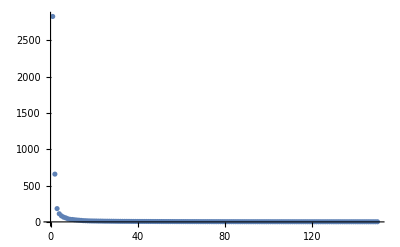

```mathematica
ee=Table[ei[[i]],{i,1,Min[JJ,150]}];
ListPlot[ee,PlotRange->All]
```

```mathematica
Sum[ei[[i]],{i,1,80}]/Sum[ei[[i]],{i,1,JJ}]
```

0.924985

```mathematica
U=-Transpose[Eigenvectors[c]];
MatrixForm[U];
```

```mathematica
z=-X.U;
```

```mathematica
tam=Round[II*0.75]
```

274

```mathematica
NEi=200;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];
```

```mathematica
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
```

```mathematica
NEiR=40;
LtraiR=Table[Take[Ltrai[[i,1]],NEiR]->Ltrai[[i,2]],{i,1,Length[Ltrai]}];LtestR=Table[Take[Ltest[[i,1]],NEiR]->Ltest[[i,2]],{i,1,Length[Ltest]}];CL=Classify[LtraiR, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
sum=0;
Do[If[CL[LtestR[[i,1]]]==LtestR[[i,2]],sum=sum+1],{i,1,Length[LtestR]}];
N[sum/Length[LtestR]]
```

0.934066

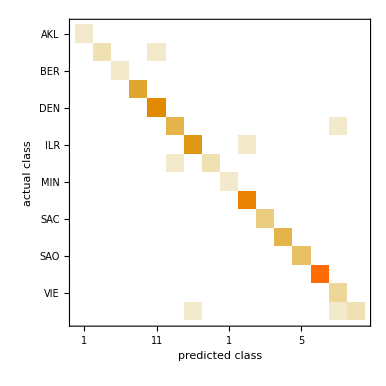

```mathematica
ClassifierMeasurements[CL,LtestR,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierMeasurements[CL,LtestR,{"Accuracy"}]
```

{0.934066}

```mathematica
auxGB=GatherBy[dcl,Last];
```

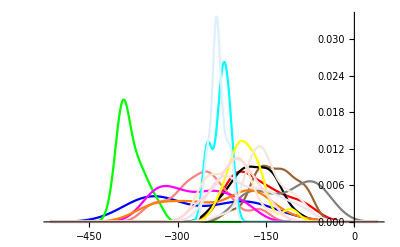

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[auxGB[[r,i,1,1]],{i,1,aux[[r,2]]}]];SmoothHistogram[Table[lf[i],{i,1,nC}],PlotRange->All,PlotStyle->COL]
```

```mathematica
COL[[4]]
```

RGBColor[0.6, 0.4, 0.2]

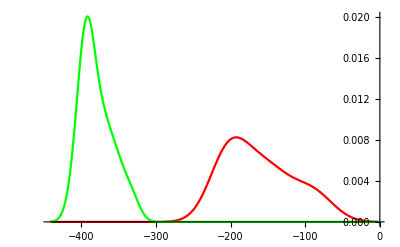

```mathematica
aa=1;
bb=3;
SmoothHistogram[{lf[aa],lf[bb]},PlotRange->All,
PlotStyle->{COL[[aa]],COL[[bb]]}]
```

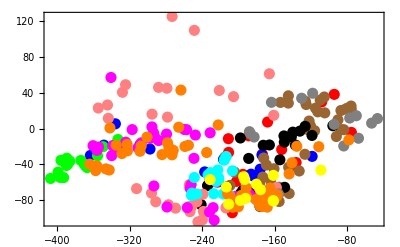

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[{auxGB[[r,i,1,1]],auxGB[[r,i,1,2]]},{i,1,aux[[r,2]]}]];
ListPlot[Table[lf[r],{r,1,11}],Frame->True,PlotStyle->Table[{COL[[i]],PointSize[0.02]},{i,1,11}],Axes->False,PlotRange->All]
```

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[{auxGB[[r,i,1,1]],auxGB[[r,i,1,2]],auxGB[[r,i,1,3]]},{i,1,aux[[r,2]]}]];
ListPointPlot3D[Table[lf[r],{r,1,nC}],PlotRange->All,PlotStyle->Table[{COL[[i]],PointSize[0.02]},{i,1,11}]]
```

-Graphics3D-

```mathematica
NEi=40;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];tt=25;
Monitor[Do[
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
CL=Classify[Ltrai,Method->"LogisticRegression"];
sum=0;
Do[If[CL[Ltest[[i,1]]]==Ltest[[i,2]],sum=sum+1],{i,1,Length[Ltest]}];
vP[k]=N[sum/Length[Ltest]],{k,1,tt}];
VPnuevo=Table[vP[k],{k,1,tt}],k];
mean=Mean[VPnuevo]
```

0.888791

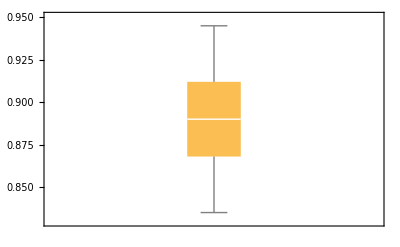

```mathematica
BoxWhiskerChart[VPnuevo]
```

```mathematica
HH=15;
Monitor[Do[
NEi=0+10*h;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];
tt=100;
Do[
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
CL=Classify[Ltrai,Method->"LogisticRegression"];
sum=0;
Do[If[CL[Ltest[[i,1]]]==Ltest[[i,2]],sum=sum+1],{i,1,Length[Ltest]}];
VP[h,k]=N[sum/Length[Ltest]],{k,1,tt}];
VPnuevo=Table[VP[h,k],{k,1,tt}];
qq=Sum[ei[[i]],{i,1,NEi}]/Sum[ei[[i]],{i,1,JJ}];
sc[h]={NEi,qq,Mean[VPnuevo]},{h,1,HH}],h]
```

```mathematica
TT=Table[Table[VP[h,k],{k,1,tt}],{h,1,HH}];
```

```mathematica
TTaux=Import["TTv2.dat","Table"];
TTjoin=Join[TTaux,Transpose[TT]];Length[Transpose[TTjoin][[1]]]
```

500

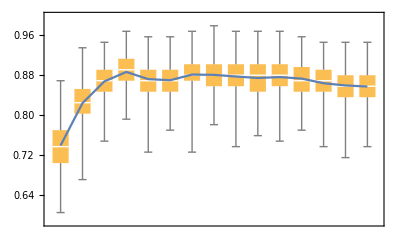

```mathematica
mTT=Table[Mean[Transpose[TTjoin][[h]]],{h,1,HH}];
g1=ListPlot[mTT,Joined->True,PlotRange->All];g2=BoxWhiskerChart[Transpose[TTjoin]];Show[g2,g1]
```

```mathematica
SC3=Table[{sc[h][[1]],sc[h][[2]],mTT[[h]]},{h,1,HH}];
TableForm[SC3]
```

10 | 0.819503 | 0.738637
20 | 0.856418 | 0.823385
30 | 0.87619 | 0.866835
40 | 0.890312 | 0.88567
50 | 0.901705 | 0.871341
60 | 0.91092 | 0.869143
70 | 0.918563 | 0.880418
80 | 0.924985 | 0.879868
90 | 0.93055 | 0.876593
100 | 0.935521 | 0.873626
110 | 0.940102 | 0.875407
120 | 0.944343 | 0.872418
130 | 0.948298 | 0.863143
140 | 0.952046 | 0.858681
150 | 0.955604 | 0.856527

```mathematica
Export["TTv2.dat",TTjoin]
```

TTv2.dat